More about Patterns

Within the Wolfram Language, there’s a whole sublanguage of patterns. We’ve already seen some of its important elements.

_ ("blank") stands for anything. x_ ("x blank") stands for anything, but calls it x. _h stands for anything with head h. And x_h stands for anything with head h, and calls it x.

Define a function whose argument is an integer named n:

```mathematica
digitback[n_Integer]:=Framed[Reverse[IntegerDigits[n]]]
```

The function evaluates whenever the argument is an integer:

```mathematica
{digitback[1234],digitback[6712],digitback[x],digitback[{4,3,2}],digitback[2^32]}
```

{{4,3,2,1},{2,1,7,6},digitback[x],digitback[{4,3,2}],{6,9,2,7,6,9,4,9,2,4}}

Sometimes you may want to put a condition on a pattern. You can do this with /; (“slash semi”). n_Integer/;n>0 means any integer that is greater than 0.

Give a definition which only applies when n>0:

```mathematica
pdigitback[n_Integer/;n>0]:=Framed[Reverse[IntegerDigits[n]]]
```

The definition doesn’t apply to negative numbers:

```mathematica
{pdigitback[1234],pdigitback[-1234],pdigitback[x],pdigitback[2^40]}
```

{{4,3,2,1},pdigitback[-1234],pdigitback[x],{6,7,7,7,2,6,1,1,5,9,9,0,1}}

The /; can go anywhere—even at the end of the whole definition.

Define different cases of the check function:

```mathematica
check[x_,y_]:=Red/;x>y
```

```mathematica
check[x_,y_]:=Green/;x≤y
```

Some examples of the check function:

```mathematica
{check[1,2],check[2,1],check[3,4],check[50,60],check[60,50]}
```

{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]}

__ (“double blank”) stands for any sequence of one or more arguments. ___ (“triple blank”) stands for zero or more.

Define a function that looks for black and white (in that order) in a list.

The pattern matches black followed by white, with any elements before, between and after them:

```mathematica
blackwhite[{___,Black,m___,White,___}]:={1,m,2,m,3,m,4}
```

Pick out the (smallest) sequence between a black and a white:

```mathematica
blackwhite[{RGBColor[1, 0.5, 0.5],GrayLevel[0],RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],GrayLevel[1]}]
```

{1,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],2,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],3,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],4}

By default, __ and ___ pick the shortest matches that work. You can use Longest to make them pick the longest instead.

Specify that the sequence between black and white should be as long as possible:

```mathematica
blackwhitex[{___,Black,Longest[m___],White,___}]:={1,m,2,m,3,m,4}
```

Now m grabs elements all the way to the last white:

```mathematica
blackwhitex[{RGBColor[1, 0.5, 0.5],GrayLevel[0],RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],GrayLevel[1]}]
```

{1,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],2,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],3,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],4}

x|y|z matches x, y or z. x.. matches any number of repetitions of x.

bwcut effectively cuts out the longest run containing only black and white:

```mathematica
bwcut[{a___,Longest[(Black|White)..],b___}]:={{a},Red,{b}}
```

```mathematica
bwcut[{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],GrayLevel[0],GrayLevel[1],GrayLevel[1],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0]}]
```

{{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5]},RGBColor[1, 0, 0],{RGBColor[1, 1, 0]}}

The pattern x_ is actually short for x:_, which means “match anything (i.e. _) and name the result x”. You can use notations like x: for more complicated patterns too.

Set up a pattern named m that matches a list of two pairs:

```mathematica
grid22[m:{{_,_},{_,_}}]:=Grid[m,Frame->All]
```

```mathematica
{grid22[{{a,b},{c,d}}],grid22[{{12,34},{56,78}}],grid22[{123,456}],grid22[{{1,2,3},{4,5,6}}]}
```

{a | b
c | d,12 | 34
56 | 78,grid22[{123,456}],grid22[{{1,2,3},{4,5,6}}]}

Name the sequence of black and white, so it can be used in the result:

```mathematica
bwcut[{a___,r:Longest[(Black|White)..],b___}]:={{a},Framed[Length[{r}]],{b}}
```

```mathematica
bwcut[{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],GrayLevel[0],GrayLevel[1],GrayLevel[1],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0]}]
```

{{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5]},5,{RGBColor[1, 1, 0]}}

As a final example, let’s use patterns to implement the classic computer science algorithm of sorting a list by repeatedly swapping pairs of successive elements that are found to be out of order. It’s easy to write each step in the algorithm as a replacement for a pattern.

Replace the first elements one finds out of order by ones that are in order:

```mathematica
{5,4,1,3,2}/.{x___,b_,a_,y___}/;b>a->{x,a,b,y}
```

{4,5,1,3,2}

Do the same operation 10 times, eventually sorting the list completely:

```mathematica
NestList[(#/.{x___,b_,a_,y___}/;b>a->{x,a,b,y})&,{4,5,1,3,2},10]
```

{{4,5,1,3,2},{4,1,5,3,2},{1,4,5,3,2},{1,4,3,5,2},{1,3,4,5,2},{1,3,4,2,5},{1,3,2,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5}}

At the beginning, we won’t know how long it’ll take to finish sorting a particular list. So the best thing is to use FixedPointList, which is like NestList, except that you don’t have to tell it a specific number of steps, and instead it just goes on until the result reaches a fixed point, where nothing more is changing.

Do the operation until a fixed point is reached:

```mathematica
FixedPointList[(#/.{x___,b_,a_,y___}/;b>a->{x,a,b,y})&,{4,5,1,3,2}]
```

{{4,5,1,3,2},{4,1,5,3,2},{1,4,5,3,2},{1,4,3,5,2},{1,3,4,5,2},{1,3,4,2,5},{1,3,2,4,5},{1,2,3,4,5},{1,2,3,4,5}}

Transpose to find the list of elements appearing first, second, etc. at successive steps:

```mathematica
Transpose[%]
```

{{4,4,1,1,1,1,1,1,1},{5,1,4,4,3,3,3,2,2},{1,5,5,3,4,4,2,3,3},{3,3,3,5,5,2,4,4,4},{2,2,2,2,2,5,5,5,5}}

ListLinePlot plots each list in a different color, showing how the sorting process proceeds:

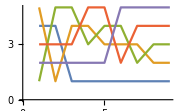

```mathematica
ListLinePlot[%]
```

Here’s the result for sorting a random length-20 list:

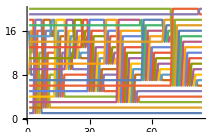

```mathematica
ListLinePlot[Transpose[FixedPointList[(#/.{x___,b_,a_,y___}/;b>a->{x,a,b,y})&,RandomSample[Range[20]]]]]
```

Vocabulary

patt/;cond |   | a pattern that matches if a condition is met
_ _ _ |   | a pattern for any sequence of zero or more elements (“triple blank”)
patt.. |   | a pattern for one or more repeats of patt
Longest[patt] |   | a pattern that picks out the longest sequence that matches
FixedPointList[f,x] |   | keep nesting f until the result no longer changes

"12 Exercises Available" | "Get Started »"

Find the list of digits for squares of numbers less than 100 that contain successive repeated digits. »

| Expected output: |  
  | {{1,0,0},{1,4,4},{2,2,5},{4,0,0},{4,4,1},{9,0,0},{1,1,5,6},{1,2,2,5},{1,4,4,4},{1,6,0,0},{2,1,1,6},{2,2,0,9},{2,5,0,0},{3,3,6,4},{3,6,0,0},{3,8,4,4},{4,2,2,5},{4,4,8,9},{4,9,0,0},{5,7,7,6},{6,4,0,0},{6,8,8,9},{7,2,2,5},{7,7,4,4},{8,1,0,0},{8,8,3,6},{1,0,0,0,0}} |

In the first 100 Roman numerals, find those containing L, I and X in that order. »

| Expected output: |  
  | {"XLIX","LIX","LXIX","LXXIX","LXXXIX"} |

Define a function f that tests whether a list of integers is the same as its reverse. »

Get a list of pairs of successive words in the Wikipedia article on alliteration that have identical first letters. »

| Sample expected output: |  
  | {{"same","sounds"},{"or","of"},{"stressed","syllables"},{"alphabet","and"},{"to","the"},{"to","the"},{"lazy","languid"},{"Peter","Piper"},{"Piper","Picked"},{"Pickled","Peppers"},{"wind","will"},{"agreement","akin"},{"to","the"},{"stressed","syllable"},{"as","alliterating"},{"of","outside"},{"same","sound"},{"of","outside"},{"to","the"},{"brown","blazers"},{"fundamentally","for"},{"colour","co-ordination"},{"in","its"},{"silken","sad"},{"furrow","followed"},{"followed","free"},{"stood","still"},{"Alphabetical","Africa"},{"chapter","consists"},{"at","all"},{"written","with"},{"Brent","Bernard"},{"who","watch"},{"watch","with"},{"with","wild"},{"wild","wonder"},{"wide","window"},{"beautiful","birds"},{"birds","begin"},{"bountiful","birdseed"},{"Grey","Geese"},{"grey","geese"},{"Betty","Botter"},{"Betty","Botter"},{"butter","but"},{"she","said"},{"butter's","bitter"},{"it","in"},{"make","my"},{"batter","bitter"},{"bitter","but"},{"better","butter"},{"make","my"},{"bitter","batter"},{"batter","better"},{"Peter","Piper"},{"Piper","Peter"},{"Peter","Piper"},{"pickled","peppers"},{"Peter","Piper"},{"pickled","peppers"},{"pickled","peppers"},{"Peter","Piper"},{"Irish","It"},{"important","ingredient"},{"Æthelwulf","Æthelbald"},{"Æthelbald","Æthelberht"},{"direct","descendants"},{"Tancred","Torhtred"},{"poetry","poets"},{"can","call"},{"splendid","silent"},{"silent","sun"},{"Walt","Whitman"},{"Splendid","Silent"},{"Silent","Sun"},{"wondered","what"},{"his","horse"},{"also","add"},{"to","the"},{"harsh","hard"},{"they","than"},{"slippered","sleep"},{"lean","lithe"},{"fleet","flown"},{"E.","E."},{"an","artistic"},{"that","the"},{"out","of"},{"as","an"},{"an","artistic"},{"constraint","can"},{"it","is"},{"emotional","effect"},{"as","a"},{"and","attention"},{"as","a"},{"persuasive","public"},{"any","attitude"},{"as","a"},{"adds","a"},{"an","audience’s"},{"audience’s","attention"},{"noticeable","nature"},{"evokes","emotion"},{"an","audience"},{"them","to"},{"to","the"},{"can","create"},{"is","in"},{"twenty-one","times"},{"times","throughout"},{"as","an"},{"which","we"},{"our","only"},{"of","our"},{"our","own"},{"but","by"},{"today","that"},{"that","the"},{"truths","that"},{"is","inextricably"},{"to","the"},{"itself","is"},{"testimony","to"},{"to","the"},{"have","had"},{"because","brave"},{"freedom's","front"},{"Ronald","Reagan"},{"Vietnam","Veterans"},{"new","nation"},{"to","the"},{"modern","music"},{"cartoon","characters"},{"If","I"},{"Anadiplosis","Assonance"},{"Tautogram","Tongue"},{"alliterations","and"}} |

Use Grid to show the sorting process in this section for {4,5,1,3,2}, with successive steps going down the page. »

| Expected output: |  
  | 4 | 5 | 1 | 3 | 2
4 | 1 | 5 | 3 | 2
1 | 4 | 5 | 3 | 2
1 | 4 | 3 | 5 | 2
1 | 3 | 4 | 5 | 2
1 | 3 | 4 | 2 | 5
1 | 3 | 2 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5 |

Use ArrayPlot to show the sorting process in this section for a list of length 50, with successive steps going across the page. »

| Sample expected output: |  
  | -Graphics- |

Start with 1.0, then repeatedly apply the “Newton’s method” function (#+2/# )/2& until the result no longer changes. »

| Expected output: |  
  | {1.,1.5,1.41667,1.41422,1.41421,1.41421,1.41421} |

Implement Euclid’s algorithm for GCD in which {a,b} is repeatedly replaced by {b,Mod[a,b]} until b is 0, and apply the algorithm to 12345, 54321. »

| Expected output: |  
  | {{12345,54321},{54321,12345},{12345,4941},{4941,2463},{2463,15},{15,3},{3,0},{3,0}} |

Define combinators using the rules s[x_][y_][z_]→x[z][y[z]],k[x_][y_]→x, then generate a list by starting with s[s][k][s[s[s]][s]][s] and applying these rules until nothing changes. »

| Expected output: |  
  | {s[s][k][s[s[s]][s]][s],s[s[s[s]][s]][k[s[s[s]][s]]][s],s[s[s]][s][s][k[s[s[s]][s]][s]],s[s][s][s[s]][s[s[s]][s]],s[s[s]][s[s[s]]][s[s[s]][s]],s[s][s[s[s]][s]][s[s[s]][s[s[s]][s]]],s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s]][s[s[s]][s]]]],s[s[s[s]][s[s[s]][s]]][s[s][s[s[s]][s[s[s]][s]]][s[s[s[s]][s[s[s]][s]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s]][s[s[s]][s]][s[s[s[s]][s[s[s]][s]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]][s[s[s[s]][s[s[s]][s]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]]} |

Remove all trailing 0’s from the digit list for 100!. »

| Expected output: |  
  | {9,3,3,2,6,2,1,5,4,4,3,9,4,4,1,5,2,6,8,1,6,9,9,2,3,8,8,5,6,2,6,6,7,0,0,4,9,0,7,1,5,9,6,8,2,6,4,3,8,1,6,2,1,4,6,8,5,9,2,9,6,3,8,9,5,2,1,7,5,9,9,9,9,3,2,2,9,9,1,5,6,0,8,9,4,1,4,6,3,9,7,6,1,5,6,5,1,8,2,8,6,2,5,3,6,9,7,9,2,0,8,2,7,2,2,3,7,5,8,2,5,1,1,8,5,2,1,0,9,1,6,8,6,4} |

Start from {1,0} then for 200 steps repeatedly remove the first 2 elements, and append {0,1} if the first element is 1 and {1,0,0} if it is 0 and get a list of the lengths of the sequences produced (tag system). »

| Expected output: |  
  | {2,2,3,3,4,4,5,6,6,7,8,9,9,10,11,11,12,12,13,13,14,14,15,16,16,17,17,18,19,19,20,21,22,22,23,23,24,24,25,25,26,26,27,28,29,29,30,30,31,32,32,33,33,34,35,35,36,37,37,38,38,39,40,40,41,42,43,43,44,44,45,45,46,46,47,47,48,48,49,50,50,51,52,53,53,54,55,55,56,56,57,58,58,59,59,60,61,61,62,62,63,64,64,65,66,67,67,68,69,69,70,70,71,71,72,72,73,74,74,75,76,77,77,78,78,79,79,80,80,81,82,82,83,84,85,85,86,87,87,88,88,89,89,90,90,91,92,92,93,93,94,95,95,96,97,98,98,99,100,100,101,101,102,103,103,104,104,105,106,106,107,108,109,109,110,111,111,112,112,113,113,114,114,115,116,116,117,117,118,119,119,120,121,122,122,123,123,124,124,125,125} |

Start from {0,0} then for 200 steps repeatedly remove the first 2 elements, and append {2,1} if the first element is 0, {0} if the first element is 1, and {0,2,1,2} if it is 2, and make a line plot of the lengths of the sequences produced (tag system). »

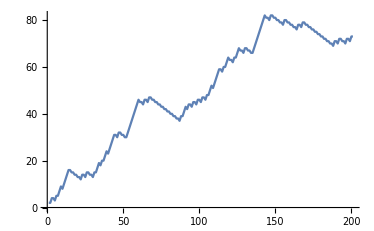
| Expected output: |  
  | -Graphics- |

Q&A

What are other pattern constructs in the Wolfram Language?

Except[patt] matches anything except patt. PatternSequence[patt] matches a sequence of arguments in a function. OrderlessPatternSequence[patt] matches them in any order. f[x_:v] defines v as a default value, so f[ ] is matched, with x being v.

How can one see all the ways a pattern could match a particular expression?

Use ReplaceList. Replace gives the first match; ReplaceList gives a list of all of them.

What does FixedPointList do if there’s no fixed point?

It’ll eventually stop. There’s an option that tells it how far to go. FixedPointList[f,x,n] stops after at most n steps.

Tech Notes

In a repeating pattern patt.., don’t forget to leave a space in e.g. 0 .. to avoid confusion with decimal numbers.

Functions can have attributes that affect how pattern matching works. For example, Plus has attributes Flat and Orderless. Flat means that b+c can be pulled out of a+b+c+d. Orderless means that elements can be reordered, so a+c can be pulled out. (Flat is like the mathematical property of associativity; Orderless like commutativity.)

The algorithm for sorting shown is usually called bubble sort. For a list of length n, it’ll typically take about n^2 steps. The built-in Wolfram Language function Sort is much faster, and takes only a little over n steps.

More to Explore

Guide to Patterns in the Wolfram Language »